# Metastable states?

### Parallel lines code

Let’s do two parallel lines. 
    M= total number of sites. 
    L= sites per layer = M/2.
    H1 = Hamiltonian for first layer.
    H2 = Hamiltonian for second layer.
    H12 = Hamiltonian between layers.
    Hp = Hamiltonian for parallel layers
    InterLayerCoupling = coupling strength between lines

```mathematica
Id={{1,0},{0,1}};
Sx=(1/2) {{0,1},{1,0}};
Sy=(1/2) {{0,-I},{I,0}};
Sz=(1/2) {{1,0},{0,-1}};
h=KroneckerProduct[Sx,Sx]+KroneckerProduct[Sy,Sy]+KroneckerProduct[Sz,Sz]-1/4 KroneckerProduct[Id,Id];
(*The function hRand[s] creates a random local XXZ operator between two sites where the anisotropry paramater Delta is normally distributed with mean 1 and standard deviation 1*)
hRand[σ_]:=KroneckerProduct[Sx,Sx]+KroneckerProduct[Sy,Sy]+If[σ<= 0, 1,RandomVariate[NormalDistribution[1,σ]] ](KroneckerProduct[Sz,Sz]-1/4 KroneckerProduct[Id,Id]);
vec[x_,L_]:=Table[If[EvenQ[Floor[k/2^(L-x)]],1,0],{k,0,2^L-1}]
(*The functions "OnePtBottom" and "OnePtTop" compute the 1-point functions for the Bottom and Top lines, respectively, for a collection of states evs.*)
OnePtBottom[k_,evs_,M_,L_,keepIndices_]:=Module[{Evec,norm,table,j},Evec=evs[[k]]//N;
norm=Norm[Evec]^2;
Evec=Map[Function[x,Abs[x]^2],Evec];
table=Table[{j,N[Dot[Evec,vec[j,M][[keepIndices]]]/norm]},{j,1,L}];
Return[table]]
OnePtTop[k_,evs_,M_,L_,keepIndices_]:=Module[{Evec,norm,table,j},Evec=evs[[k]]//N;
norm=Norm[Evec]^2;
Evec=Map[Function[x,Abs[x]^2],Evec];
table=Table[{j,N[Dot[Evec,vec[L+j,M][[keepIndices]]]/norm]},{j,1,L}];
Return[table]]
(*REMARK:I've changed the "ParallelLines" function to add an inhomogeneous magnetic field B with max stength b and random XXZ anisotropy parameters Δ with Normal distributions centered at 1 and with standard deviation σ.*)
ParallelLines[M_,L_,InterLayerCoupling_, b_, σ_]:=Module[{H1,H2,H12, B,basis,keepIndices,Hp,trimmedHp},
B= Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], ((L-k)/(L-1))b Sz, IdentityMatrix[2^(M-k)]], {k, 1, L}] +Sum[KroneckerProduct[IdentityMatrix[2^(L-1+k)], (1/2)((L-k)/(L-1))b Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}];
H1 =  Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hRand[σ], IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], hRand[σ], IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}];
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ (Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M]);
Hp = -H1 - H2 + (InterLayerCoupling*H12) + B;

basis = Table[IntegerDigits[2^M-k, 2,M], {k ,1, 2^M}];
(* We consider the case where half the spins are flipped. I.e. ferromagnetic within the layer, antiferromagnetic between layers. Ultimately, we want to evolve the state where one spin in each layer is flipped *)
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==L]];
trimmedHp = N[Hp[[keepIndices,keepIndices]]];
Return[{trimmedHp, keepIndices}]
]
WaveFunction[Eigenvalues_,Eigenvectors_,ConfigurationIndex_,t_,hbar_]:=Sum[Eigenvectors[[k]][[ConfigurationIndex]]*Exp[-I*Eigenvalues[[k]]*t/hbar]*Eigenvectors[[k]],{k,1,Length[Eigenvectors]}]
```

```mathematica
WaveFunction[Eigenvalues_,Eigenvectors_,ConfigurationIndex_,t_,hbar_]:=Module[{n,Λ, i, j, U, Uct, state},
n= Length[Eigenvalues];
Λ = Table[If[i==j, Exp[-I*Eigenvalues[[i]]*t/hbar], 0], {i,1, n}, {j, 1, n}];
U =Eigenvectors;
Uct= ConjugateTranspose[U];
state= Table[If[i==ConfigurationIndex, 1, 0], {i, 1, n}];
Return[Uct.Λ.U.state];
]
```

### Parallel line code: L=3, J_intra=1/10, σ =0

```mathematica
L=3;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0,0];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(-0.15 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.95 | -0.5 | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 1.45 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0.85 | 0. | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0. | 1.45 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0. | -0.5 | 1.85 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.45 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.
0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.95 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 1.45 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.5 | 0.85 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0.05
0.05 | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.85 | -0.5 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.45 | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0.95 | 0. | 0. | 0. | 0. | 0. | 0.05 | 0.
0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.45 | -0.5 | 0. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.85 | -0.5 | 0. | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.45 | 0. | 0. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | 0. | 0.85 | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.45 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | -0.5 | 0.95 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.15)

{8,12,14,15,20,22,23,26,27,29,36,38,39,42,43,45,50,51,53,57}

```mathematica
Eigs = Eigenvalues[Hp];
```

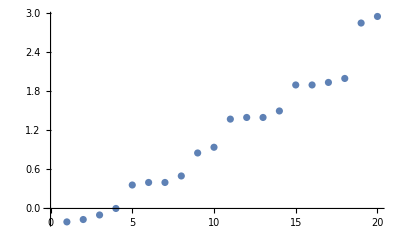

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

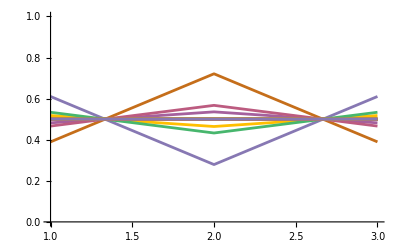

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}}]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
MatrixForm[NEVecs]
MatrixForm[Chop[ConjugateTranspose[NEVecs].NEVecs]]
```

(0.0114019 | 0.123673 | -0.241633 | 0.128885 | -0.241633 | 0.450013 | -0.241633 | 0.123673 | -0.241633 | 0.128885 | 0.128885 | -0.241633 | 0.123673 | -0.241633 | 0.450013 | -0.241633 | 0.128885 | -0.241633 | 0.123673 | 0.0114019
-0.0112952 | -0.122561 | 0.239338 | -0.105482 | 0.239338 | -0.467382 | 0.239338 | 0.122561 | -0.239338 | 0.105482 | -0.105482 | 0.239338 | -0.122561 | -0.239338 | 0.467382 | -0.239338 | 0.105482 | -0.239338 | 0.122561 | 0.0112952
2.82098×10^-16 | -0.288675 | 0.288675 | 5.03434×10^-15 | 0.288675 | 1.51091×10^-16 | -0.288675 | -0.288675 | 0.288675 | -1.20865×10^-14 | -4.83971×10^-15 | -0.288675 | 0.288675 | 0.288675 | 1.25965×10^-16 | -0.288675 | 1.23384×10^-14 | -0.288675 | 0.288675 | 7.87906×10^-18
1.02369×10^-16 | -1.77956×10^-14 | 0.300375 | -0.263722 | -0.300375 | -1.28381×10^-16 | 0.300375 | 2.42741×10^-15 | -0.300375 | 0.263722 | 0.263722 | -0.300375 | 1.8078×10^-14 | 0.300375 | 6.30345×10^-17 | -0.300375 | -0.263722 | 0.300375 | -2.4666×10^-15 | -1.01298×10^-17
1.59542×10^-16 | 0.102309 | 0.167629 | -0.269938 | -0.372246 | -3.67546×10^-17 | 0.372246 | -0.102309 | 0.372246 | -0.269938 | 0.269938 | -0.167629 | -0.102309 | -0.167629 | 9.41647×10^-17 | 0.167629 | 0.269938 | -0.372246 | 0.102309 | 1.20043×10^-17
-1.27983×10^-16 | 0.269938 | -0.372246 | 0.102309 | -0.167629 | -4.66768×10^-16 | 0.167629 | -0.269938 | 0.167629 | 0.102309 | -0.102309 | 0.372246 | -0.269938 | 0.372246 | 5.06668×10^-16 | -0.372246 | -0.102309 | -0.167629 | 0.269938 | 3.56826×10^-18
3.41675×10^-17 | 5.67322×10^-16 | -0.353553 | -2.79459×10^-16 | 0.353553 | -3.55787×10^-16 | 0.353553 | 6.72247×10^-16 | 0.353553 | -1.91007×10^-18 | 1.88916×10^-16 | -0.353553 | 1.4678×10^-16 | -0.353553 | -9.53632×10^-16 | -0.353553 | 2.75646×10^-16 | 0.353553 | 7.36526×10^-17 | -2.06029×10^-17
4.64075×10^-16 | -0.0253465 | -0.33883 | -0.0253465 | 0.364176 | 0.0506931 | 0.364176 | 0.0253465 | -0.364176 | 0.0253465 | -0.0253465 | -0.33883 | -0.0253465 | 0.33883 | -0.0506931 | 0.33883 | 0.0253465 | -0.364176 | 0.0253465 | 1.09637×10^-17
-4.461×10^-17 | -0.234335 | 0.155188 | -0.234335 | 0.0791479 | 0.468671 | 0.0791479 | 0.234335 | -0.0791479 | 0.234335 | -0.234335 | 0.155188 | -0.234335 | -0.155188 | -0.468671 | -0.155188 | 0.234335 | -0.0791479 | 0.234335 | -1.48484×10^-18
-0.00452339 | 0.283999 | -0.106387 | 0.172753 | -0.106387 | -0.483434 | -0.106387 | 0.283999 | -0.106387 | 0.172753 | 0.172753 | -0.106387 | 0.283999 | -0.106387 | -0.483434 | -0.106387 | 0.172753 | -0.106387 | 0.283999 | -0.00452339
-0.0310015 | 0.316909 | 0.0185039 | -0.380587 | 0.0185039 | 0.0843433 | 0.0185039 | 0.316909 | 0.0185039 | -0.380587 | -0.380587 | 0.0185039 | 0.316909 | 0.0185039 | 0.0843433 | 0.0185039 | -0.380587 | 0.0185039 | 0.316909 | -0.0310015
0.0342224 | -0.361383 | -0.0167242 | 0.343885 | -0.0167242 | -0.000773971 | -0.0167242 | 0.361383 | 0.0167242 | -0.343885 | 0.343885 | -0.0167242 | -0.361383 | 0.0167242 | 0.000773971 | 0.0167242 | -0.343885 | 0.0167242 | 0.361383 | -0.0342224
-1.00906×10^-16 | -0.408248 | -0.204124 | 8.45257×10^-16 | -0.204124 | 1.25897×10^-17 | 0.204124 | -0.408248 | -0.204124 | 1.24421×10^-15 | -7.52423×10^-16 | 0.204124 | 0.408248 | -0.204124 | -4.78745×10^-18 | 0.204124 | -1.08725×10^-15 | 0.204124 | 0.408248 | 0.
-2.38297×10^-16 | -0.0842008 | -0.241836 | -0.399471 | 0.157635 | 4.61073×10^-17 | -0.157635 | 0.0842008 | -0.157635 | -0.399471 | 0.399471 | 0.241836 | 0.0842008 | 0.241836 | -1.09713×10^-16 | -0.241836 | 0.399471 | 0.157635 | -0.0842008 | -6.75324×10^-17
-1.32232×10^-17 | -0.399471 | -0.157635 | 0.0842008 | -0.241836 | 2.02713×10^-16 | 0.241836 | 0.399471 | 0.241836 | 0.0842008 | -0.0842008 | 0.157635 | 0.399471 | 0.157635 | 1.05394×10^-16 | -0.157635 | -0.0842008 | -0.241836 | -0.399471 | 8.31516×10^-18
-3.58801×10^-16 | 1.13303×10^-15 | -0.186479 | -0.424795 | 0.186479 | 2.93525×10^-17 | -0.186479 | -1.3774×10^-15 | 0.186479 | 0.424795 | 0.424795 | 0.186479 | -1.29881×10^-15 | -0.186479 | 1.10514×10^-17 | 0.186479 | -0.424795 | -0.186479 | 1.57923×10^-15 | 7.28404×10^-17
-0.4987 | 0.145078 | 0.160533 | 0.193089 | 0.160533 | 0.177634 | 0.160533 | -0.145078 | -0.160533 | -0.193089 | 0.193089 | 0.160533 | 0.145078 | -0.160533 | -0.177634 | -0.160533 | -0.193089 | -0.160533 | -0.145078 | 0.4987
0.669991 | -0.0601513 | -0.0703778 | -0.0932652 | -0.0703778 | -0.0816473 | -0.0703778 | -0.0601513 | -0.0703778 | -0.0932652 | -0.0932652 | -0.0703778 | -0.0601513 | -0.0703778 | -0.0816473 | -0.0703778 | -0.0932652 | -0.0703778 | -0.0601513 | 0.669991
-0.5 | -0.166667 | -0.166667 | -0.166667 | -0.166667 | -0.166667 | -0.166667 | 0.166667 | 0.166667 | 0.166667 | -0.166667 | -0.166667 | -0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.166667 | 0.5
0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607 | 0.223607)

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,2,t,1]],{t,0,100,0.2}];
```

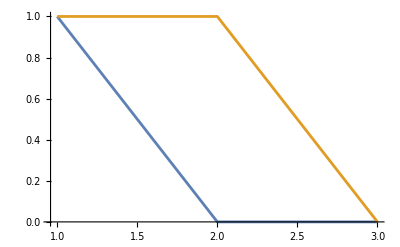

```mathematica
OnePtWaveTop=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
OnePtWaveBottom=Table[OnePtBottom[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
ListPlot[{OnePtWaveTop[[1]],OnePtWaveBottom[[1]] }, Joined->True]
```

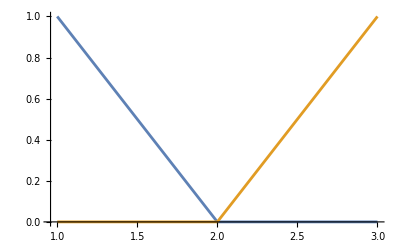

```mathematica
inv =Table[{0, 1}, {k,1,L}] ;
OnePtWaveBottom=Map[Function[x,Abs[inv-x]],OnePtWaveBottom];
ListPlot[{OnePtWaveTop[[1]],OnePtWaveBottom[[1]] }, Joined->True]
```

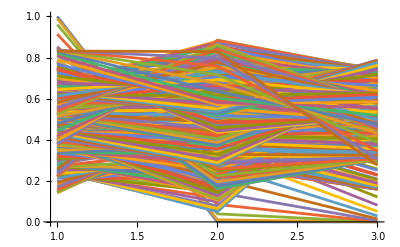

```mathematica
ListPlot[OnePtWaveTop, Joined->True]
```

```mathematica
Animate[ListPlot[{OnePtWaveTop[[t]], OnePtWaveBottom[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

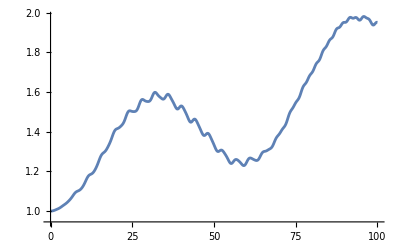

```mathematica
(*A plot of the expected number of up-spins on the top layer as a function of time. Let's think about this plot and make sure that it makes sense*)
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

### Parallel line code: L=3, J_intra=1/10

```mathematica
L=3;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(-0.15 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.949669 | -0.5 | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 1.44934 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0.849544 | 0. | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0. | 1.44904 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0. | -0.5 | 1.84872 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.44892 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.
0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.949052 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 1.44885 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.5 | 0.849176 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0.05
0.05 | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.849176 | -0.5 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.44885 | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0.949052 | 0. | 0. | 0. | 0. | 0. | 0.05 | 0.
0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.44892 | -0.5 | 0. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.84872 | -0.5 | 0. | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.44904 | 0. | 0. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | 0. | 0.849544 | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.44934 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | -0.5 | 0.949669 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.15)

{8,12,14,15,20,22,23,26,27,29,36,38,39,42,43,45,50,51,53,57}

```mathematica
Eigs = Eigenvalues[Hp];
```

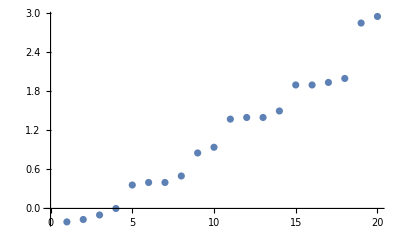

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

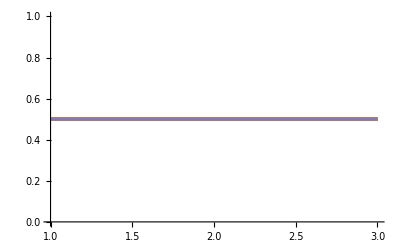

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,M,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

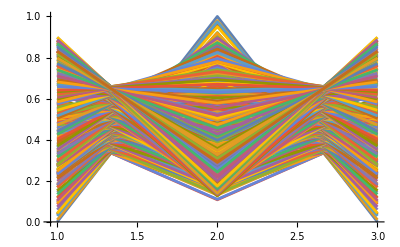

```mathematica
ListPlot[OnePtWave, Joined->True]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

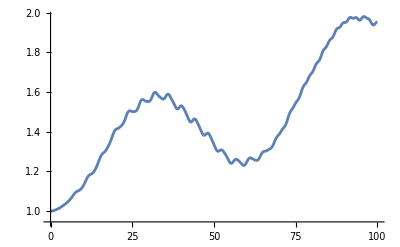

```mathematica
(*A plot of the expected number of up-spins on the top layer as a function of time. Let's think about this plot and make sure that it makes sense*)
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

### Parallel line code: L=3, J_intra=0

```mathematica
L=3;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,0,0, 1/1000];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.00096 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 1.50167 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 1.00116 | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0. | 1.50006 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 0. | -0.5 | 2.00076 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.50025 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999796 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 1.5003 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0.999598 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.999598 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.5003 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0.999796 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.50025 | -0.5 | 0. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 2.00076 | -0.5 | 0. | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.50006 | 0. | 0. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 1.00116 | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.50167 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.00096 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

{8,12,14,15,20,22,23,26,27,29,36,38,39,42,43,45,50,51,53,57}

```mathematica
Eigs = Eigenvalues[Hp];
```

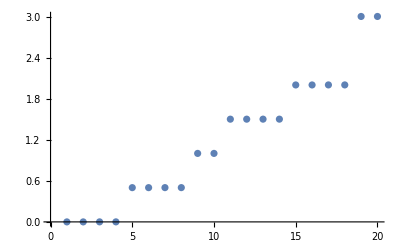

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

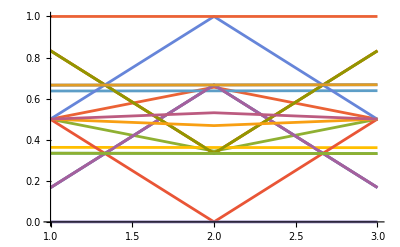

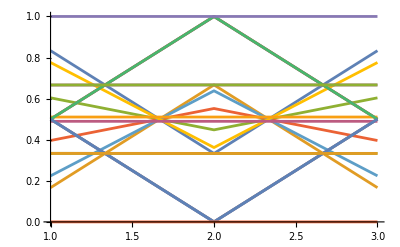

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,M,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWaveDC=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

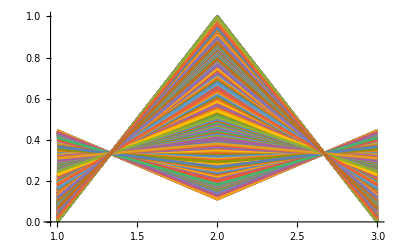

```mathematica
ListPlot[OnePtWaveDC, Joined->True]
```

```mathematica
Animate[ListPlot[OnePtWaveDC[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWaveDC], 1}]
```

```mathematica
Animate[ListPlot[{OnePtWaveDC[[t]], OnePtWave[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWaveDC], 1}]
```

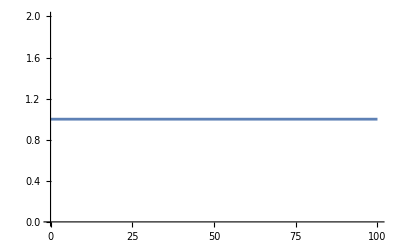

```mathematica
ListPlot[Table[{(t-1)*0.2,Sum[OnePtWaveDC[[t]][[k]][[2]],{k,1,L}]},{t,1,Length[OnePtWaveDC]}],Joined->True]
```

### Parallel line code: L=4, J_intra=1/10

```mathematica
L=4;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
Eigs = Eigenvalues[Hp];
```

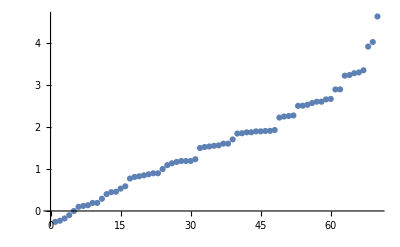

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

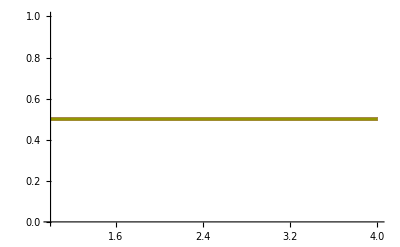

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,8,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
OnePtWave2=Table[OnePtBottom[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
(*The following operation keeps track of the down-spin the bottom layer instead of the up-spin.*)
inv =Table[{0, 1}, {k,1,L}] ;
OnePtWave2=Map[Function[x,Abs[inv-x]],OnePtWave2];
```

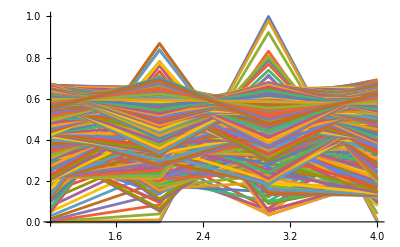

```mathematica
ListPlot[OnePtWave, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ OnePtWave2[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

```mathematica
(*Plots of the one-point functions for the top and a bottom layer. The plots seem to match well through time.*)
Animate[ListPlot[ {OnePtWave[[t]],OnePtWave2[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

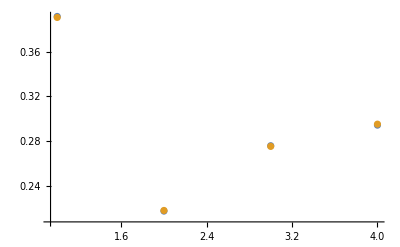

{{1,0.391526},{2,0.217582},{3,0.275967},{4,0.294397}}

{{1,0.390637},{2,0.218141},{3,0.275415},{4,0.29528}}

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

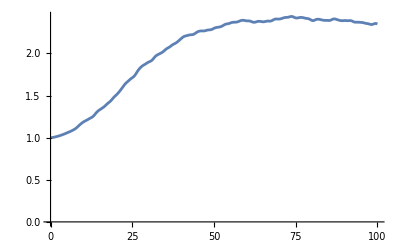

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

### Parallel line code: L=4, J_intra=0

```mathematica
L=4;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,0,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
Eigs = Eigenvalues[Hp];
```

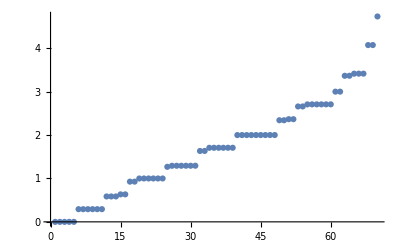

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

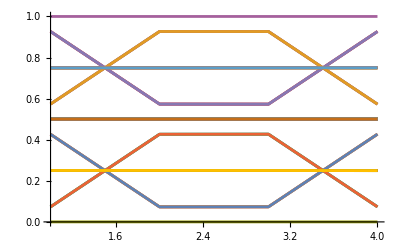

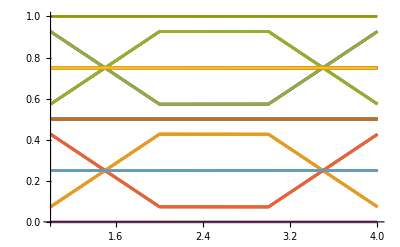

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecsUC = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
EvaluationUC = Table[Chop[WaveFunction[Eigs,NEVecsUC ,8,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWaveUC=Table[OnePtTop[k,EvaluationUC,M,L,keepIndices],{k,1,Length[EvaluationUC]}];
```

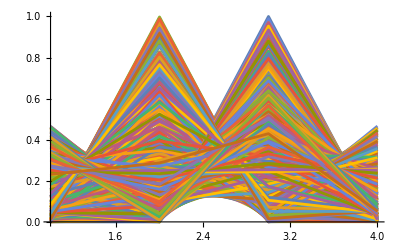

```mathematica
ListPlot[OnePtWaveUC, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWaveUC[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ {OnePtWave[[t]],OnePtWaveUC[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

-Graphics-

{{1,0.391526},{2,0.217582},{3,0.275967},{4,0.294397}}

{{1,0.390637},{2,0.218141},{3,0.275415},{4,0.29528}}

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

-Graphics-

### Parallel line code: L=5, J_intra=1/10

```mathematica
L=5;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{32,48,56,60,62,63,80,88,92,94,95,104,108,110,111,116,118,119,122,123,125,144,152,156,158,159,168,172,174,175,180,182,183,186,187,189,200,204,206,207,212,214,215,218,219,221,228,230,231,234,235,237,242,243,245,249,272,280,284,286,287,296,300,302,303,308,310,311,314,315,317,328,332,334,335,340,342,343,346,347,349,356,358,359,362,363,365,370,371,373,377,392,396,398,399,404,406,407,410,411,413,420,422,423,426,427,429,434,435,437,441,452,454,455,458,459,461,466,467,469,473,482,483,485,489,497,528,536,540,542,543,552,556,558,559,564,566,567,570,571,573,584,588,590,591,596,598,599,602,603,605,612,614,615,618,619,621,626,627,629,633,648,652,654,655,660,662,663,666,667,669,676,678,679,682,683,685,690,691,693,697,708,710,711,714,715,717,722,723,725,729,738,739,741,745,753,776,780,782,783,788,790,791,794,795,797,804,806,807,810,811,813,818,819,821,825,836,838,839,842,843,845,850,851,853,857,866,867,869,873,881,900,902,903,906,907,909,914,915,917,921,930,931,933,937,945,962,963,965,969,977,993}

```mathematica
Eigs = Eigenvalues[Hp];
```

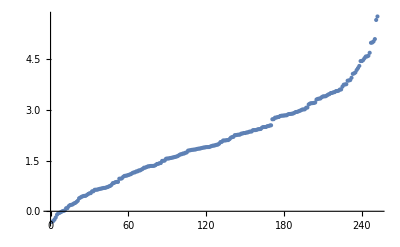

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

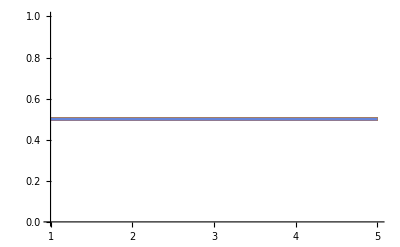

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,24,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
OnePtWave2=Table[OnePtBottom[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
inv =Table[{0, 1}, {k,1,L}] ;
OnePtWave2=Map[Function[x,Abs[inv-x]],OnePtWave2];
```

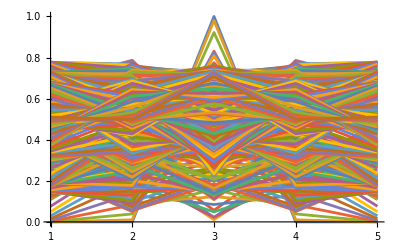

```mathematica
ListPlot[OnePtWave, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ OnePtWave2[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

```mathematica
Animate[ListPlot[ {OnePtWave[[t]],OnePtWave2[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

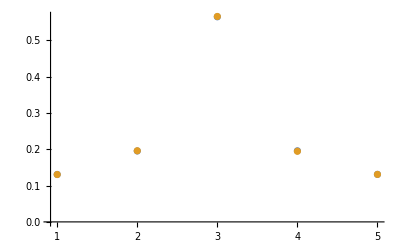

{{1,0.130675},{2,0.195429},{3,0.565189},{4,0.195883},{5,0.130913}}

{{1,0.130553},{2,0.196033},{3,0.566102},{4,0.194526},{5,0.130875}}

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

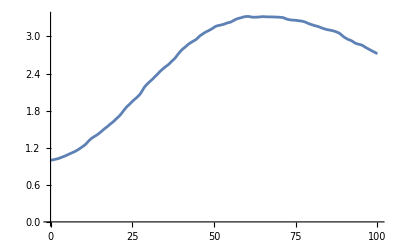

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```